```mathematica
Manipulate[
Plot[a*(x)^3 + b*(x)^2 + c*(x) + d,{x, 0, 100}, 
PlotRange->{0,800}], {a, -1,1}, {b, -10, 10}, 
{c,-10,10}, {d, 0, 100}]
```

```mathematica
Reduce[{
125a+25b+5c+d == 70,
30a + 2b >0 ,
75a + 10b + c == 0,
3375000a + 22500b + 150c +d == 700}, 
{a,b,c,d}]
```

a<126/609725&&b==(126-672800 a)/4205&&c==-75 a-10 b&&d==70-125 a-25 b-5 c

a < 126/609725 && b == (126 - 672800*a)/4205 && c == -75*a - 10*b && d == 70 - 125*a - 25*b - 5*c

WolframAlphaQueryResults

```mathematica
FindInstance[a<126/609725&&b==(126-672800 a)/4205&&c==-75 a-10 b&&d==70-125 a-25 b-5 c,{a,b,c,d}]
```

{{a→-17,b→11437726/4205,c→-21803177/841,d→53673250/841}}

```mathematica
NSolve[a<126/609725&&b==(126-672800 a)/4205&&c==-75 a-10 b&&d==70-125 a-25 b-5 c,{a,b,c,d}]
```

NSolve::svars: Equations may not give solutions for all "solve" variables.

{{a→ConditionalExpression[1.48633×10^-6 (126.-4205. b),Re[b]>-0.00309976&&Im[b]==0],c→ConditionalExpression[-0.000111474 (126.-4205. b)-10. b,Re[b]>-0.00309976&&Im[b]==0],d→ConditionalExpression[70.-0.000185791 (126.-4205. b)-5. (-0.000111474 (126.-4205. b)-10. b)-25. b,Re[b]>-0.00309976&&Im[b]==0]}}

```mathematica
Manipulate[
Plot[
y= a*(x-5)^2+50, {x,0,200}],
{a,0,0.1}
]
```

```mathematica
plot1=
Plot[
y= 0.0168*(x-5)^2+50, {x,0,210}, PlotStyle->Red]

plot2=
Plot[
y=(10 (x-5))/3 + 50, {x,0,210},PlotStyle->Blue]

Show[plot1,plot2]
```

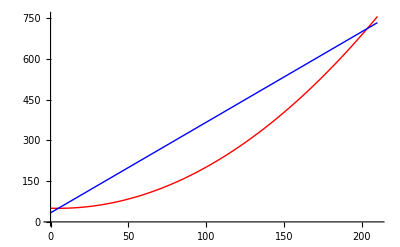

```mathematica
9
```